```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
std=StandardDeviation@portfolio[[All,2]];
return=Last@portfolio[[All,2]];
{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All],{return,std,return/std}//TableForm[#,TableHeadings->{{"return","std","r/s"},Automatic}]&}
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Wed 22 Feb 2017

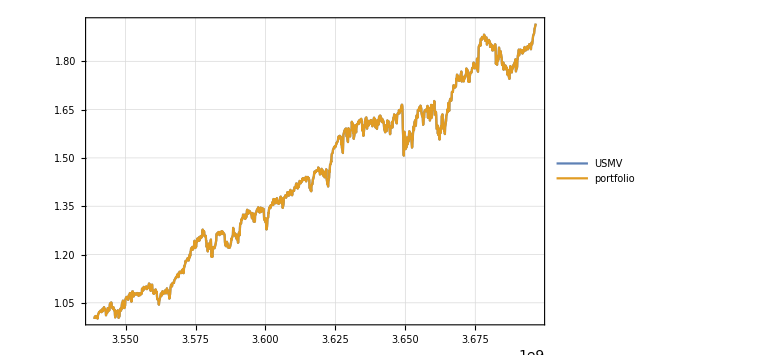
{-Graphics-,return | 1.91694
std | 0.26108
r/s | 7.34237}

```mathematica
PortfolioChart[{"USMV"},start,end]
```

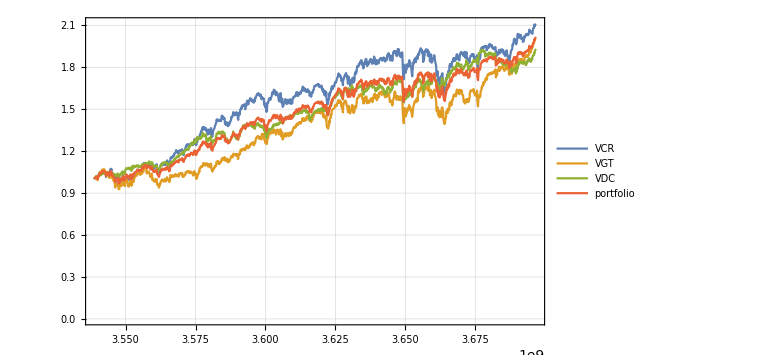
{-Graphics-,return | 2.01712
std | 0.28385
r/s | 7.10631}

```mathematica
PortfolioChart[{"VCR","VGT","VDC"},start,end]
```

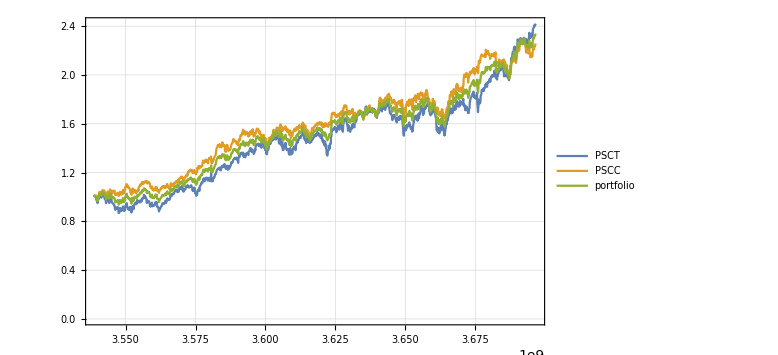
{-Graphics-,return | 2.33868
std | 0.357249
r/s | 6.54636}

```mathematica
PortfolioChart[{"PSCT","PSCC"},start,end]
```

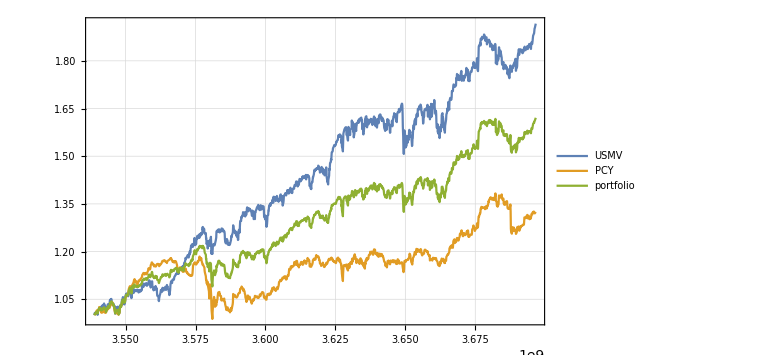
{-Graphics-,return | 1.62085
std | 0.168843
r/s | 9.59976}

```mathematica
PortfolioChart[{"USMV","PCY"},start,end]
```

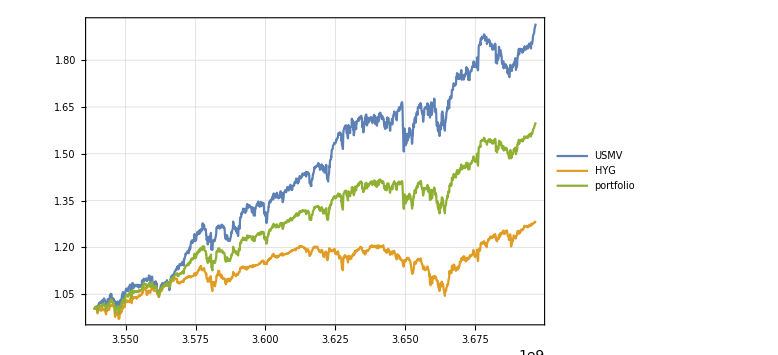
{-Graphics-,return | 1.60074
std | 0.159651
r/s | 10.0265}

```mathematica
PortfolioChart[{"USMV","HYG"},start,end]
```

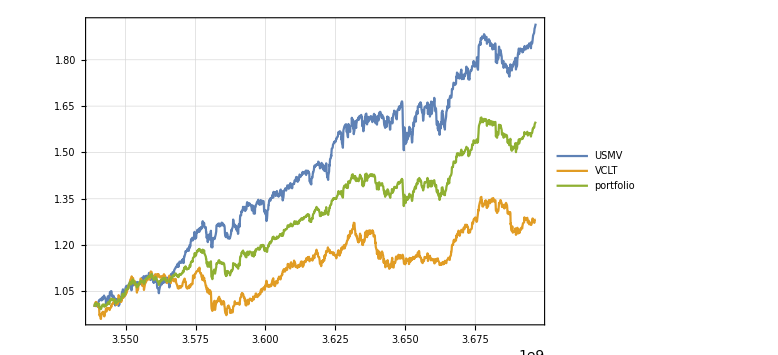
{-Graphics-,return | 1.59959
std | 0.173943
r/s | 9.19603}

```mathematica
PortfolioChart[{"USMV","VCLT"},start,end]
```

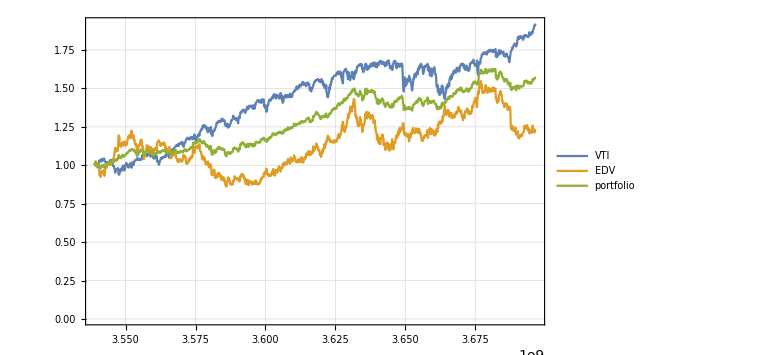
{-Graphics-,return | 1.5733
std | 0.184236
r/s | 8.5396}

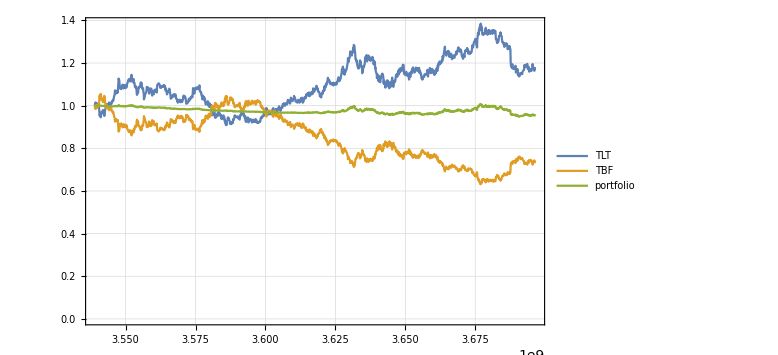
{-Graphics-,return | 0.955533
std | 0.0128282
r/s | 74.4871}

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

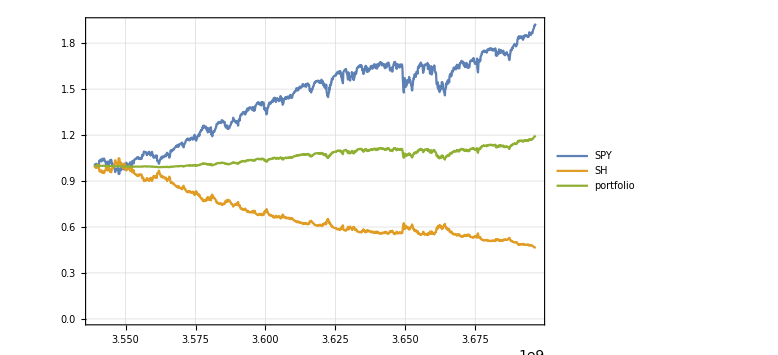
{-Graphics-,return | 1.1952
std | 0.0512059
r/s | 23.3411}

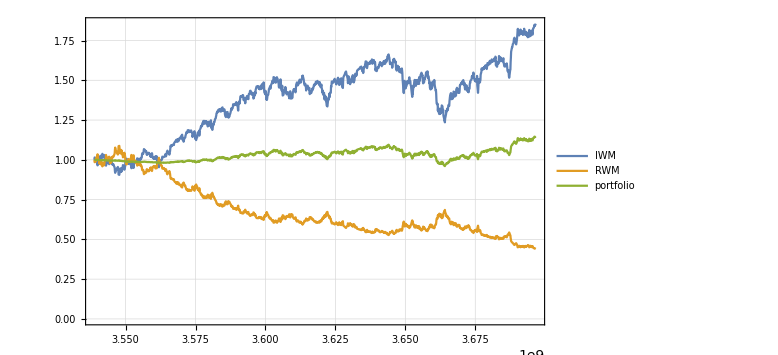
{-Graphics-,return | 1.14803
std | 0.0368345
r/s | 31.1672}

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

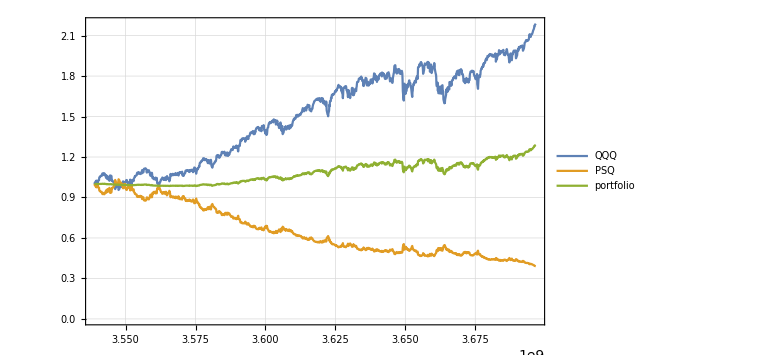
{-Graphics-,return | 1.28949
std | 0.0785359
r/s | 16.4191}

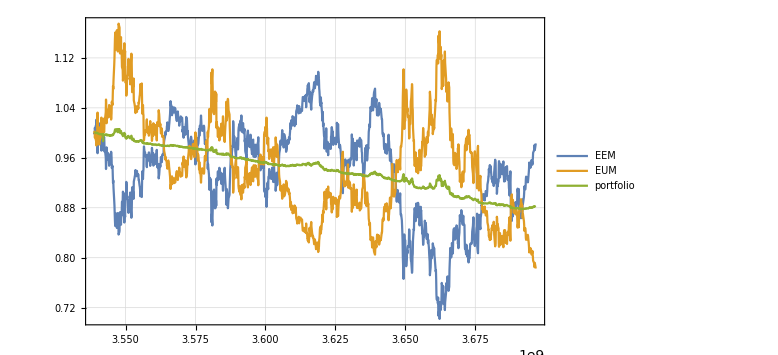
{-Graphics-,return | 0.882853
std | 0.0353563
r/s | 24.9701}

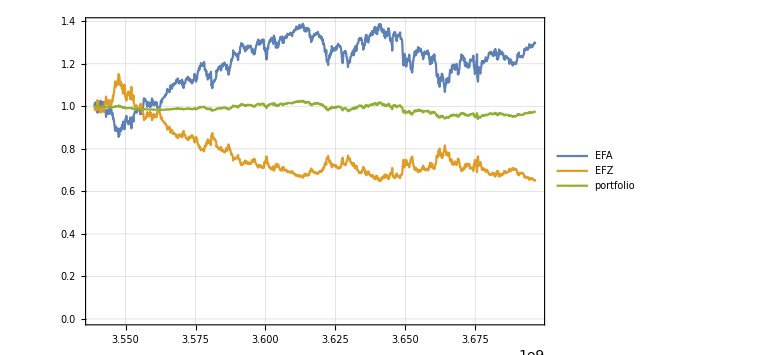
{-Graphics-,return | 0.975199
std | 0.0191253
r/s | 50.99}

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```